```mathematica
foo::bar="This is a message with parameters `1` and `2`.";
```

```mathematica
Message[foo::bar,"this","that"]
```

foo::bar: This is a message with parameters this and that.

```mathematica
FullForm[%2]
```

Image3D

```mathematica
Messages[foo]
```

{HoldPattern[foo::bar]:>This is a message with parameters `1` and `2`.}

```mathematica
Off[foo::bar]
```

```mathematica
Message[foo::bar,"ain't gonna","happen"]
```

```mathematica
On[foo::bar]
```

```mathematica
Message[foo::bar,"I am","back"]
```

foo::bar: This is a message with parameters I am and back.

```mathematica
$Messages
```

{OutputStream[…]}

```mathematica
msglog=OpenWrite["msglog"];
Block[{$Messages=Append[$Messages,msglog]},
Message[foo::bar,"superman","superhero"];]
Close[msglog];
```

foo::bar: This is a message with parameters superman and superhero.

```mathematica
$Messages
```

{OutputStream[…],OutputStream[msglog,3]}

```mathematica
$Messages=Drop[$Messages,-1]
```

Options::optnf: 
   FormatType is not a known option for OutputStream[msglog, 3].

{OutputStream[…]}

```mathematica
$Messages
```

{OutputStream[…]}

```mathematica
FilePrint[msglog[[1]]]
```

foo::bar: This is a message with parameters superman and superhero.

the user can control message parameter formatting by assigning a function.

```mathematica
Message[foo::bar,Range[1000],"that wasn't so bad"]
```

foo::bar: This is a message with parameters {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«950»} and that wasn't so bad.

```mathematica
Block[{$MessagePrePrint=TeXForm},Message[foo::bar,a^2/b^2,Sin[theta]]]
```

foo::bar: This is a message with parameters \frac{a^2}{b^2} and \sin (\theta ).

```mathematica
example[func_]:=Check[Integrate[func,{x,1,Infinity}],$Failed]
```

```mathematica
example[1/x^2]
```

1

```mathematica
example[1/x]
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

$Failed

```mathematica
$MessageList
```

{}

```mathematica
Check[Integrate[1/x,{x,1,Infinity}],If[MemberQ[$MessageList,HoldForm[Integrate::idiv]],"the integral does not converge","something wrong."]]
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

the integral does not converge

```mathematica
MessageList[41]
```

{Integrate::idiv}

```mathematica
$Line
```

43

```mathematica
General::argbu
```

`1` called with 1 argument; between `2` and `3` arguments are expected.

```mathematica
Message[foo::argbu,"foo",3,4]
```

foo::argbu: foo called with 1 argument; between 3 and 4 arguments are expected.

```mathematica
Messages[General]
```

{HoldPattern[General::appname]:>The name `1` is not valid for the application. A valid name starts with a letter and is followed by letters and digits.,HoldPattern[General::argbu]:>`1` called with 1 argument; between `2` and `3` arguments are expected.,HoldPattern[General::bktwrn]:>"`1`" represents multiplication; use "`2`" to represent a function`4`.,HoldPattern[General::catname]:>The name `1` is not valid for the category. A valid name starts with a letter and is followed by letters and digits.,HoldPattern[General::file]:>The preferences file `1` is not a file.,HoldPattern[General::fsfq]:>Unexpected state reached in `1`.,HoldPattern[General::fstr]:>File specification `1` is not a string of one or more characters.,HoldPattern[General::infy]:>Infinite expression `1` encountered.,HoldPattern[General::meprec]:>Internal precision limit $MaxExtraPrecision = `1` reached while evaluating `2`.,HoldPattern[General::newsym]:>$Off[],HoldPattern[General::nfunfail]:>$Off[],HoldPattern[General::nofirst]:>`1` has zero length and no first element.,HoldPattern[General::nosite]:>Site `1` is not an existing Paclet site.,HoldPattern[General::obspkgfn]:>$Off[],HoldPattern[General::offline]:>The Wolfram Language is currently configured not to use the Internet. To allow Internet use, check the "Allow the Wolfram Language to use the Internet" box in the Help ▶ Internet Connectivity dialog.,HoldPattern[General::oldversion]:>Connections to kernels older than Version 2.2 are not supported. This kernel is version `1`.,HoldPattern[General::pclt]:>`1` does not refer to a known paclet.,HoldPattern[General::pcltn]:>No appropriate paclet with name `1` was found.,HoldPattern[General::pcltni]:>No appropriate paclet with name `1` is installed.,HoldPattern[General::pcltnv]:>No appropriate paclet with name `1` and version `2` was found.,HoldPattern[General::pcltnvi]:>No appropriate paclet with name `1` and version `2` is installed.,HoldPattern[General::plnr]:>$Off[],HoldPattern[General::pp3tr]:>$Off[],HoldPattern[General::pptr]:>$Off[],HoldPattern[General::prefdir]:>The preferences directory `1` cannot be created.,HoldPattern[General::pwfailed]:>$Off[],HoldPattern[General::sandbox]:>$Off[],HoldPattern[General::shdw]:>Symbol `1` appears in multiple contexts `2`; definitions in context `3` may shadow or be shadowed by other definitions.,HoldPattern[General::spell]:>$Off[],HoldPattern[General::spell1]:>$Off[],HoldPattern[General::stop]:>Further output of `1` will be suppressed during this calculation.,HoldPattern[General::sysmain]:>Error loading the main binary file `1`.
	 Get["sysmake.m"] must be run before continuing.,HoldPattern[General::writewarn]:>Defining rule for `1`.,HoldPattern[General::wrsym]:>Symbol `1` is Protected.}

```mathematica
Cases[%47,HoldPattern[General::sysmain]:>_]
```

{}

```mathematica
FullForm[%47[[1]]]
```

RuleDelayed[HoldPattern[MessageName[General,"appname"]],"The name `1` is not valid for the application. A valid name starts with a letter and is followed by letters and digits."]

```mathematica
Select[%47,MemberQ[#,"argrx",Infinity]&]
```

{}

```mathematica
FullForm[%47[[1]]]
```

RuleDelayed[HoldPattern[MessageName[General,"appname"]],"The name `1` is not valid for the application. A valid name starts with a letter and is followed by letters and digits."]

```mathematica
MemberQ[%47[[1]],"appname",Infinity]
```

True

```mathematica
MatchQ[1,1]
```

True

```mathematica
MatchQ[%47[[1]],RuleDelayed[HoldPattern[MessageName[General,"appname"]],_]]
```

False

```mathematica
MatchQ[1,1]
```

True

```mathematica
MatchQ[%47[[1]],_[_[_[_,"appname"]],_]]
```

True

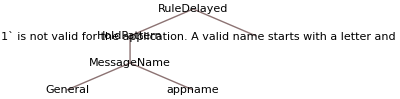
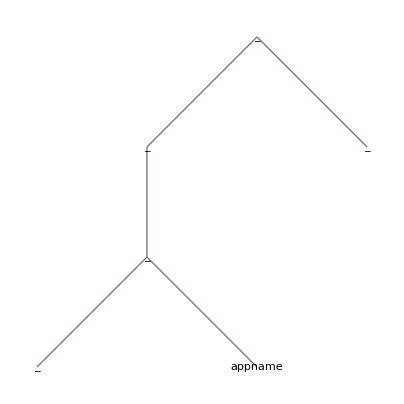

```mathematica
TreeForm/@{%47[[1]],_[_[_[_,"appname"]],_]}
```

```mathematica
HoldPattern[MessageName[a,b]]
```

HoldPattern[a::b]

```mathematica
Head[%]
```

HoldPattern

```mathematica
LCGRandom[]:="a random number"
LCGRandom[x__]:=Message[LCGRandom::argrx,"LCGRandom",Length[{x}],0]
```

```mathematica
LCGRandom[a,b]
```

LCGRandom::argrx: LCGRandom called with 2 arguments; 0 arguments are expected.

```mathematica
Clear[LCGRandom];
LCGRandom[x___]:="a random number"/;Length[{x}]==0||Message[LCGRandom::argrx,"LCGRandom",Length[{x}],0]
```

```mathematica
LCGRandom[]
```

a random number

```mathematica
LCGRandom[a,b]
```

LCGRandom::argrx: LCGRandom called with 2 arguments; 0 arguments are expected.

LCGRandom[a,b]